```mathematica
twitter=ServiceConnect["Twitter"]
```

ServiceObject[…]

```mathematica
tweetfrequency[q_]:=Module[{ds,min,max},
ds=twitter["TweetSearch","Query"-> q];
{min,max}=MinMax[Map[AbsoluteTime,Normal[ds[All,"CreationDate"]]]];
(max-min)/3600.]
```

```mathematica
tweetfrequency["chongqing"]
```

8.17111

```mathematica
tweetfrequency["chongqing"]
```

```mathematica
regions=Map[ToLowerCase[StringSplit[#["Name"],","][[1]]]&,Normal[ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"][Select[#Country["Name"]==="China"&],"AdministrativeDivision"]]]
```

{hubei,zhejiang,guangdong,henan,hunan,anhui,jiangxi,chongqing,jiangsu,sichuan,shandong,beijing,shanghai,fujian,heilongjiang,shaanxi,guangxi,hebei,yunnan,hainan,shanxi,liaoning,tianjin,guizhou,gansu,jilin,ningxia,neimenggu,xinjiang,qinghai,xizang}

```mathematica
tmp=AssociationMap[tweetfrequency,regions]
```

<|hubei→0.0797222,zhejiang→4.94306,guangdong→5.4375,henan→1.1425,hunan→4.98778,anhui→17.5567,jiangxi→16.47,chongqing→8.31528,jiangsu→17.3297,sichuan→4.43194,shandong→13.9764,beijing→0.474722,shanghai→0.386667,fujian→8.56639,heilongjiang→19.9036,shaanxi→35.6453,guangxi→2.87139,hebei→31.8414,yunnan→19.7014,hainan→11.0028,shanxi→37.9378,liaoning→92.1425,tianjin→8.55083,guizhou→27.9642,gansu→29.7642,jilin→7.99611,ningxia→55.3319,neimenggu→29.1194,xinjiang→2.00639,qinghai→112.574,xizang→185.308|>

```mathematica
Dataset[tmp][Sort]
```

```mathematica
60 60
```

3600

```mathematica
29416/3600.
```

8.17111

```mathematica
Map[CellPrint[Cell[#,"Text"]]&,Normal[ds[All,"Text"]]]
```

```mathematica
tweets=Normal[ds[All,"Text"]];
```

```mathematica
hashtags=Flatten[Map[Select[TextWords[#],StringStartsQ["#"]]&,tweets]]
```

{#coranovirus,#coronaviruswuhan,#Chongqing,#CINA,#Chongqing,#avgeek,#aviation,#aviationlovers,#avgeek,#aviation,#aviationlovers,#Zhejiang,#Guangdong,#Henan,#Hunan,#Jiangxi,#Anhui,#CINA,#Chongqing,#architecture,#building,#architexture,#buildings,#design,#art,#architecturelovers,#modernism,#beautiful,#archilovers,#architectureporn,#style,#bridge,#composition,#perspective,#china,#chongqing,#重庆市,#chinese,#szechuan,#sichuan,#四川,#cq,#中国,#PRC,#avgeek,#aviation,#aviationlovers,#coronaviruschina,#wuhan,#Chongqing,#CINA,#Chongqing,#coronavirus,#Chongqing,#chongqing,#china,#AngelJennieDay,#우리의,#JENNIE,#제니,#CINA,#Chongqing,#CINA,#Chongqing,#CINA,#Chongqing,#CINA,#Chongqing,#conoravirus,#Chongqing,#Chongqing,#Chongqing,#Chongqing,#Chongqing,#Chongqing,#Chongqing,#China,#XiaoZhan,#WangYibo,#garden,#modernism,#traditional,#trees,#view,#cityscape,#city,#urbanphotography,#architecture,#photography,#architecturephotography,#citylife,#streetphotography,#photooftheday,#skyline,#china,#chongqing,#重庆市,#chinese,#szechuan,#sichuan,#四川,#cq,#中国,#PRC,#CHINA,#Chongqing,#China,#Coronavirus,#MembersGetIt,#RewardsPoints,#FindYourRoute,#MRpoints,#ひるおび,#英語,#Wuhan,#NinePercent,#ToTheNines,#Chen,#NinePercent,#ToTheNines,#Ch,#지드래곤,#지디,#권지용,#GDRAGON,#GD,#IT,#LATEST,#WuhanPneumonia,#architecture,#姚琛,#YAOCHEN,#야오천,#R,#Coronavirus,#Cina,#Coronavirus,#Cina,#Coronavirus,#Cina,#Chongqing,#WuhanCoronavirusOutbreak,#姚琛,#YAOCHEN,#야오천,#R,#董思成,#윈윈,#winwin,#ウィンウィン,#WayV,#WeiShenV,#威神V}

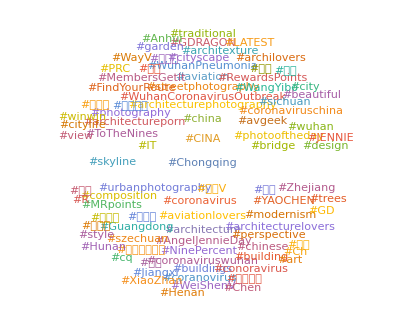

```mathematica
WordCloud[hashtags]
```

```mathematica
StringDrop["#abc",1]
```

abc

```mathematica
S
```

```mathematica
LanguageIdentify["董思成"]
```

Chinese

```mathematica
Select[hashtags,LanguageIdentify[StringDrop[#,1]]===Entity["Language","Chinese"]&]
```

```mathematica
Map[
TextTranslation[StringDrop[#,1],Entity["Language","Chinese"],Method->"Google"]&,{"#重庆市","#四川","#中国","#重庆市","#四川","#中国","#英語","#姚琛","#姚琛","#董思成","#威神V"}]
```

IntegratedServices`IntegratedServices::unexp: This service is currently not available. Please try again in a few minutes.

General::stop: Further output of IntegratedServices`IntegratedServices::unexp will be suppressed during this calculation.

{TextTranslation[重庆市,Chinese,Method→Google],TextTranslation[四川,Chinese,Method→Google],TextTranslation[中国,Chinese,Method→Google],TextTranslation[重庆市,Chinese,Method→Google],TextTranslation[四川,Chinese,Method→Google],TextTranslation[中国,Chinese,Method→Google],TextTranslation[英語,Chinese,Method→Google],TextTranslation[姚琛,Chinese,Method→Google],TextTranslation[姚琛,Chinese,Method→Google],TextTranslation[董思成,Chinese,Method→Google],TextTranslation[威神V,Chinese,Method→Google]}

```mathematica
CloudConnect[]
```

arnoudb@wolfram.com

```mathematica
Map[LanguageIdentify[StringDrop[#,1]]&,hashtags]//Union
```

{Chinese,English,Esperanto,Finnish,German,Hungarian,Italian,Japanese,Korean,Spanish,Vietnamese}